# Processing Moon

```mathematica
ccFile = "/Users/jamieinfinity/Projects/StoryTelling/Moon/moon-faye-xvid.txt";
screenDir = "/Users/jamieinfinity/Projects/StoryTelling/Moon/screens/";
```

## Functions

### Process closed captioning data

```mathematica
convertTimestampToSec[x_]:=(#[[1]]*3600+#[[2]]*60+#[[3]])&@(ToExpression/@StringSplit[x,":"]);
makeStartStop[x_]:=convertTimestampToSec/@StringSplit[x," --> "];

extractCCData0[x_]:=Module[{s1, startStop,text,i,f},
s1=StringSplit[x,"\n"];
startStop=makeStartStop[s1[[2]]];
i=startStop[[1]];
f=startStop[[2]];
text=StringJoin[Riffle[s1[[3;;-1]],"\n"]];
Return[{{{i/60//Floor,Mod[i,60]},f-i}, text}]
];

extractCCData[file_]:=Module[{ccText, ccList, ccData},
ccText=Import[file,"Plaintext"];
ccList=StringReplace[#,RegularExpression["(\\d\\d),(\\d\\d\\d)"]:>"$1.$2"]&/@StringSplit[ccText, RegularExpression["\n\n"]];
ccData=extractCCData0/@ccList;
Return[ccData];
];
```

### Load images

```mathematica
cropImage[x_]:=Module[{yshift, height},
yshift=61;
height=355;
ImageTake[x,{yshift, yshift + height}]
];

frameRate= 24.385(* 29.97003 *);
secondsBetweenFrames=1.0/frameRate;
convertFrameToSeconds[frameNumber_]:=secondsBetweenFrames*frameNumber-4;

extractFrameNumber[file_]:=ToExpression[StringReplace[file,RegularExpression[".+e(\\d+).jpeg"]:>"$1"]];

getFrames[dir_]:=Module[{screenFiles, frames},
screenFiles=FileNames["*.jpeg",{dir}];
screenFiles = #[[2]]&/@SortBy[{extractFrameNumber[#],#}&/@screenFiles,#[[1]]&];
frames=SortBy[{extractFrameNumber[#],convertFrameToSeconds[extractFrameNumber[#]],cropImage[Import[#]]}&/@screenFiles,#[[1]]&];
frames={#[[1]],#[[2]],#[[3]],ImageResize[#[[3]],{180}]}&/@frames;
Return[frames];
]
```

### Image processing

#### Gaussian kernel smoother

```mathematica
kernelFunction[x_,radius_]:=Exp[-(x^2)/(2*radius^2)]/(Sqrt[2*Pi]*radius)

smooth0[index_,x_,val_,radius_]:=Module[{numerator,denominator},
 numerator=Table[val[[i]]*kernelFunction[x[[index]]-x[[i]],radius],{i,1,Length[val]}];
 denominator=Table[kernelFunction[x[[index]]-x[[i]],radius],{i,1,Length[val]}];
Total[numerator]/Total[denominator]
];
DataSmoother[data_,radius_,diffOp_]:=Module[{x0,x,val,smoothVals},
x0=data[[1,1]];
x=N/@Round[Abs[QuantityMagnitude@diffOp[x0,#]]]&/@data[[All,1]];(* Identity was Round for dates *)
val=N/@data[[All,2]];
smoothVals=Table[smooth0[i,x,val,radius],{i,1,Length[val]}];
Transpose[{data[[All,1]],smoothVals}]
];
```

```mathematica
Integrate[1.0*kernelFunction[x,1],{x,-10,10}]
```

1.

#### Group frames into similar shots

```mathematica
findImageNeighborDistances[frameInfo_]:=Module[{coarseImages, imageDistances},
coarseImages=Blur[#,2]&@LocalAdaptiveBinarize[ImageResize[#,{360}],10]&/@frameInfo[[All,3]];
imageDistances=MapThread[ImageDistance[##,DistanceFunction->"EarthMoverDistance"]&,{Most[coarseImages],Rest[coarseImages]}];
Return[Transpose[{Range[Length[imageDistances]],imageDistances}]];
]

findShotGroups[frameInfo_]:=Module[{imageDist,imageDistSmooth,groups},
imageDist=findImageNeighborDistances[frameInfo];
imageDistSmooth=DataSmoother[imageDist,4,Subtract];
groups=Split[MapIndexed[{#2[[1]],#1}&,#[[2]]-#[[1]]&/@Transpose[{imageDistSmooth[[All,2]],imageDist[[;;,2]]}]],#1[[2]]<0&]/.{x_Integer,_}:>x;
Return[groups];
]
```

Peak behind the algorithm:

```mathematica
frames=getFrames[screenDir];
```

```mathematica
imDist=findImageNeighborDistances[frames[[1;;500]]];
imDistSm=DataSmoother[imDist,4,Subtract];
```

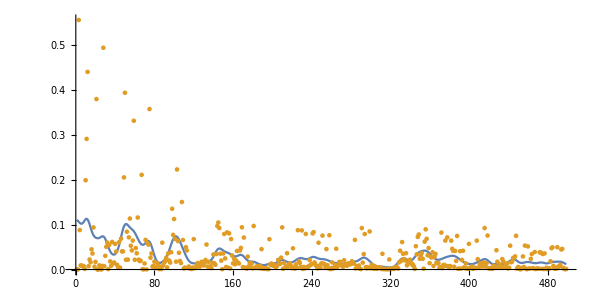

```mathematica
(* ListPlot[{ids,Tooltip[#,images[[#[[1]];;#[[1]]+1]]]&/@id[[1;;500]]},ImageSize->1500,AspectRatio->0.3,PlotRange->All] *)
ListPlot[{imDistSm,imDist},ImageSize->600,AspectRatio->0.5,PlotRange->All,Joined->{True,False}]
```

#### Curation grids

Create

```mathematica
makeElement[frame_,i_]:=Module[{row=i[[1]],f=frame[[1]],imageSm=frame[[-1]],imageLg=frame[[-2]]},
Column[{Tooltip[Show[{imageSm}], Row[{f,Show[imageLg]}]],Row[{PopupMenu[row*10,10*Range[row-5,row+5]], PopupMenu[row*10,Range[10*row-8,10*row+8,2]]}]}]
];

makeShotGrid[frames_,shotGroups_]:=Module[{shotGrid},
shotGrid = MapIndexed[makeElement[frames[[#1]],#2]&,shotGroups,{2}];
shotGrid = MapIndexed[Join[{#2[[1]]*10},#1]&,shotGrid];
Return[
Grid[shotGrid,
Frame->All,FrameStyle->LightGray,ItemSize->{{4}}]
];
];
```

```mathematica
makeElement2[frame_,i_]:=Module[{row=i[[1]],f=frame[[1]],imageSm=frame[[-1]],imageLg=frame[[-2]]},
Column[{Tooltip[Show[{imageSm}], Row[{f,Show[imageLg]}]],Row[{Checkbox[]}]}]
];

makeShotGrid2[shots_]:=Module[{shotGrid},
shotGrid = MapIndexed[makeElement2[#1,#2]&,shots,{2}];
shotGrid = MapIndexed[Join[{#2[[1]]*10},#1]&,shotGrid];
Return[
Grid[shotGrid,
Frame->All,FrameStyle->LightGray,ItemSize->{{4}}]
];
];
```

Process

```mathematica
extractFrameGroupId[_,Null]:=Null
extractFrameGroupId[rowNum_,cell_]:=Module[{d,frameId,p1,p2,groupId},
d=cell[[1]];
frameId=d[[1]][[2]][[1]][[1]];
p1=d[[2]][[1]][[1]][[1]];
p2=d[[2]][[1]][[2]][[1]];
groupId=If[p2==rowNum,p1,p2];
{frameId,groupId}
];
extractGroupIdsFromRow[row_]:=Module[{rowNum},
rowNum=row[[1]];
Cases[extractFrameGroupId[rowNum,#]&/@Rest[row],{_Integer,_Integer}]
];
extractGroupIdsFromGrid[grid_]:=Module[{},
Flatten[extractGroupIdsFromRow/@grid[[1]],1]
];
```

```mathematica
extractCellData[Null]:={0,False}
extractCellData[cell_]:=Module[{d,frameId,cb},
d=cell[[1]];
frameId=d[[1]][[2]][[1]][[1]];
cb=d[[2]][[1,1]][[1]];
{frameId,cb}
];
extractCellDataFromRow[row_]:=Module[{rowNum},
rowNum=row[[1]];
Cases[extractCellData/@Rest[row],{x_,True}:>x]
];
extractCellDataFromGrid[grid_]:=Module[{},
extractCellDataFromRow/@grid[[1]]
];
```

## Process Film Data

### Load data

```mathematica
ccData=extractCCData[ccFile];
```

```mathematica
ccData[[500]]//Column[#,Frame->All,FrameStyle->LightGray]&
```

{{42,11.676},2.127}
You're a fucking clone.
You don't have shit.

```mathematica
frames=getFrames[screenDir];
```

```mathematica
frames[[105]]
```

{3121,123.989,-Graphics-,-Graphics-}

### Curate shot groups

#### Make curation grids

```mathematica
shotGroups=findShotGroups[frames];
```

```mathematica
frames//Length
```

4551

```mathematica
shotGroups//Length
```

1399

```mathematica
4551/1399.0
```

3.25304

```mathematica
preGrid1=makeShotGrid[frames, shotGroups[[1;;200]]];
preGrid2=makeShotGrid[frames, shotGroups[[201;;400]]];
preGrid3=makeShotGrid[frames, shotGroups[[401;;600]]];
preGrid4=makeShotGrid[frames, shotGroups[[601;;800]]];
preGrid5=makeShotGrid[frames, shotGroups[[801;;1000]]];
preGrid6=makeShotGrid[frames, shotGroups[[1001;;1200]]];
preGrid7=makeShotGrid[frames, shotGroups[[1201;;1399]]];
```

#### Process curation grids

```mathematica
curatedGroups=Flatten[{
extractGroupIdsFromGrid[postGrid1],
extractGroupIdsFromGrid[postGrid2]/.{x_Integer,y_Integer}:>{x,y+2000},
extractGroupIdsFromGrid[postGrid3]/.{x_Integer,y_Integer}:>{x,y+4000},
extractGroupIdsFromGrid[postGrid4]/.{x_Integer,y_Integer}:>{x,y+6000},
extractGroupIdsFromGrid[postGrid5]/.{x_Integer,y_Integer}:>{x,y+8000},
extractGroupIdsFromGrid[postGrid6]/.{x_Integer,y_Integer}:>{x,y+10000},
extractGroupIdsFromGrid[postGrid7]/.{x_Integer,y_Integer}:>{x,y+12000}
}
,1];
```

```mathematica
curatedGroups/.{x_Integer,y_Integer}:>y//Union//Length
```

1033

```mathematica
1000/200
```

5

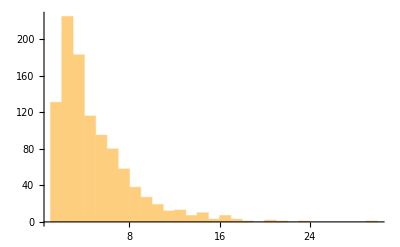

```mathematica
gL=(Length[#]&)/@GatherBy[curatedGroups,#[[2]]&];
Histogram[gL,PlotRange->All]
```

```mathematica
Mean[gL]*1.25
```

5.50581

```mathematica
5500/3600.
```

1.52778

```mathematica
Export["/Users/jamieinfinity/Projects/StoryTelling/Moon/frameGroups.csv",curatedGroups];
```

### Collect shot info

```mathematica
curatedShots=Import["/Users/jamieinfinity/Projects/StoryTelling/Moon/frameGroups.csv",HeaderLines->1];
```

```mathematica
frameRules=(#[[1]]->#)&/@frames;
```

```mathematica
shots=(First/@#)&/@SortBy[SortBy[#,#[[1]]&]&/@GatherBy[curatedShots,#[[2]]&],#[[-1,-1]]&]/.frameRules;
```

```mathematica
shots[[55]]
```

{{7531,304.837,-Graphics-,-Graphics-},{7561,306.068,-Graphics-,-Graphics-},{7591,307.298,-Graphics-,-Graphics-},{7621,308.528,-Graphics-,-Graphics-}}

```mathematica
dt=Differences@Flatten[shots[[1;;3]],1][[1;;10,2]]//First
```

1.23026

```mathematica
getTimeInfo[row_]:=Module[{i,f},
i=row[[1,2]];
f=row[[-1,2]]+dt;
{{i/60//Floor,Mod[i,60]},f-i}
]
```

```mathematica
shotTimeInfo=getTimeInfo/@shots;
```

### Curate representative shot images

```mathematica
shots//Length
```

1033

```mathematica
preRepShotGrid1=makeShotGrid2[shots[[1;;200]]];
preRepShotGrid2=makeShotGrid2[shots[[201;;400]]];
preRepShotGrid3=makeShotGrid2[shots[[401;;600]]];
preRepShotGrid4=makeShotGrid2[shots[[601;;800]]];
preRepShotGrid5=makeShotGrid2[shots[[801;;1033]]];
```

### Process representative shot image grids

```mathematica
curatedRepShots=Flatten[{
extractCellDataFromGrid[postRepShotGrid1],
extractCellDataFromGrid[postRepShotGrid2],
extractCellDataFromGrid[postRepShotGrid3],
extractCellDataFromGrid[postRepShotGrid4],
extractCellDataFromGrid[postRepShotGrid5]
}
,1];
```

```mathematica
curatedRepShots[[1;;10]]
```

{{1},{121},{601},{781},{841,901,991,1081},{1111,1171,1261},{1351,1381,1411},{1531,1591,1621,1651,1741},{1801,1831,1861},{1981}}

```mathematica
Export["/Users/jamieinfinity/Projects/StoryTelling/Moon/repShots.wl",curatedRepShots]
```

/Users/jamieinfinity/Projects/StoryTelling/Moon/repShots.wl

```mathematica
Length[curatedRepShots]
```

1033

### Merge dialog with shot info

```mathematica
curatedRepShots=Import["/Users/jamieinfinity/Projects/StoryTelling/Moon/repShots.wl",HeaderLines->1];
```

```mathematica
repShots=curatedRepShots/.frameRules;
```

```mathematica
findDialogForShot[shotTime_,ccData_]:=Module[{t1,t2},
t1=shotTime[[1]][[1]]*60+shotTime[[1]][[2]];
t2=t1+shotTime[[2]];
Select[ccData,Between[{t1,t2}][#[[1,1]][[1]]*60+#[[1,1]][[2]]+2.3]&]
]
```

```mathematica
findDialogForShot[shotTimeInfo[[149]],ccData]
```

{}

```mathematica
mergedShotInfo=Table[{"time"->shotTimeInfo[[i]],"dialog"->findDialogForShot[shotTimeInfo[[i]],ccData],"shots"->repShots[[i]]},{i,1,Length[shotTimeInfo]}];
```

```mathematica
mergedShotInfo[[149]]
```

{time→{{13,10.7919},14.7632},dialog→{},shots→{{19471,794.483,-Graphics-,-Graphics-}}}

### Curate scene/sequence info

```mathematica
makeSceneGridRow[row_]:=Module[{t,d,s},
t="time"/.row;
d="dialog"/.row;
s="shots"/.row;
{TextString[TimeObject[Join[{0},t[[1]]]],TimeFormat->{"Minute",":","Second"}],Show@Graphics[Rectangle[{0,0},{.1,t[[2]]/5}],ImageSize->10],Round@t[[2]],Column[Tooltip[Show[{#[[4]]}], Row[{f,Show[#[[3]]]}]]&/@s],Column[d[[All,2]]],InputField["",String,FieldSize->80]}
];
makeSceneGrid[shotInfo_]:=Module[{},
makeSceneGridRow/@shotInfo//Grid[#,Frame->All,FrameStyle->LightGray]&
]
```

```mathematica
preSceneGrid=makeSceneGrid[mergedShotInfo];
```

### Process scene/sequence info

```mathematica
mergedShotInfo[[3]]
```

{time→{{0,9.57392},12.3026},dialog→{},shots→{{601,20.6463,-Graphics-,-Graphics-}}}

```mathematica
extractActInfo[s_]:=StringTrim@StringReplace[s,{RegularExpression["A:\\w*(.+);.+"]:>"$1",RegularExpression[".+"]:>""}];

extractSceneInfo[s_]:=StringTrim@StringReplace[s,{RegularExpression[".*S:\\w*(.+).*"]:>"$1",RegularExpression[".+"]:>""}]

extractSceneData[grid_]:=Module[{s,acts,shotToActs,scenes,shotToScenes},
s=First/@grid[[1,All,6]];
s=StringTrim/@s;
acts=extractActInfo/@s;
acts=MapIndexed[{#2[[1]],#1}&,acts];
acts=Split[acts,StringLength[#2[[2]]]==0&];
shotToActs=MapIndexed[Function[x,Rule@@{"ST_"~~ToString@(x[[1]]-3),"A_"~~ToString[#2[[1]]]}]/@#1&,Rest[acts]]//Flatten[#,1]&;
acts=First/@Rest[acts];
acts=MapIndexed[{"A_"~~ToString[#2[[1]]],#1[[2]]}&,acts];
scenes=extractSceneInfo/@s;
scenes=MapIndexed[{#2[[1]],#1}&,scenes];
scenes=Split[scenes,StringLength[#2[[2]]]==0&];
shotToScenes=MapIndexed[Function[x,Rule@@{"ST_"~~ToString@(x[[1]]-3),"SN_"~~ToString[#2[[1]]]}]/@#1&,Rest[scenes]]//Flatten[#,1]&;
scenes=First/@Rest[scenes];
scenes=MapIndexed[{"SN_"~~ToString[#2[[1]]],#1[[2]]}&,scenes];
{"Acts"->acts, "ShotToAct"->shotToActs,"Scenes"->scenes,"ShotToScene"->shotToScenes}
]
```

```mathematica
sceneData=extractSceneData[postScanGrid];
```

```mathematica
Export["/Users/jamieinfinity/Projects/StoryTelling/Moon/film_data/acts.tsv",Join[{{"act","title"}},"Acts"/.sceneData]]
```

/Users/jamieinfinity/Projects/StoryTelling/Moon/film_data/acts.tsv

```mathematica
Export["/Users/jamieinfinity/Projects/StoryTelling/Moon/film_data/scenes.tsv",Join[{{"scene","title"}},"Scenes"/.sceneData]]
```

/Users/jamieinfinity/Projects/StoryTelling/Moon/film_data/scenes.tsv

```mathematica
zeroPad[s_]:=If[StringLength[s]>5,s,StringPadLeft[s,5,"0"]]
```

```mathematica
buildShotInfo[row_,index_]:=Module[{shot,time,duration,dialog,frames,act,scene},
shot="ST_"~~ToString[index];
act=shot/.("ShotToAct"/.sceneData);
scene=shot/.("ShotToScene"/.sceneData);
time=("time"/.row)[[1]];
duration=("time"/.row)[[2]];
dialog=("dialog"/.row)[[All,-1]];
frames=zeroPad[ToString[#]]&/@(("shots"/.row)[[All,1]]);
{"shot"->shot,"act"->act,"scene"->scene,"time"->time,"duration"->duration,"frames"->frames,"dialog"->dialog}
]
```

```mathematica
finalShotInfo=MapIndexed[buildShotInfo[#1,#2[[1]]]&,mergedShotInfo[[4;;-1]]];
```

```mathematica
Export["/Users/jamieinfinity/Projects/StoryTelling/Moon/film_data/shots.json",finalShotInfo]
```

/Users/jamieinfinity/Projects/StoryTelling/Moon/film_data/shots.json

```mathematica
sceneToAct=DeleteDuplicates[{"scene","act"}/.finalShotInfo];
```

```mathematica
Export["/Users/jamieinfinity/Projects/StoryTelling/Moon/film_data/sceneToAct.tsv",Join[{{"scene","act"}},sceneToAct]]
```

/Users/jamieinfinity/Projects/StoryTelling/Moon/film_data/sceneToAct.tsv

### Save shot images

```mathematica
fr={zeroPad[ToString[#[[1]]]],#[[2,3]]}&/@frameRules;
fr=Rule@@@fr;
```

```mathematica
shotData=Import["/Users/jamieinfinity/Projects/StoryTelling/Moon/film_data/shots.json"];
```

```mathematica
repFrames=Transpose[{Flatten[("frames"/.#)&/@shotData,1], Flatten[("frames"/.#)&/@shotData,1]/.fr}];
```

```mathematica
Export["/Users/jamieinfinity/Projects/StoryTelling/Moon/film_data/shot_images/shotImage_"~~#[[1]]~~".jpeg",#[[2]]]&/@repFrames;
```

```mathematica
Export["/Users/jamieinfinity/Projects/StoryTelling/Moon/film_data/shot_images/shotImageMED_"~~#[[1]]~~".jpeg",ImageResize[#[[2]],180]]&/@repFrames;
```

```mathematica
Export["/Users/jamieinfinity/Projects/StoryTelling/Moon/film_data/shot_images/shotImageSM_"~~#[[1]]~~".jpeg",ImageResize[#[[2]],90]]&/@repFrames;
```

```mathematica
ImageDimensions[ImageResize[#[[2]],180]&@repFrames[[1]]]
```

{180,89}

```mathematica
Length/@Gather["scene"/.shotData]
```

{9,7,12,4,4,5,11,5,3,5,1,7,2,14,3,31,1,5,5,6,5,2,5,1,1,5,7,2,3,15,6,7,1,8,14,9,4,4,1,3,1,9,8,14,4,3,1,10,9,10,23,1,10,3,13,7,1,27,21,3,1,2,23,12,11,24,8,12,3,10,2,4,33,2,1,30,14,6,6,6,2,1,2,12,51,1,18,2,6,5,1,2,5,21,1,8,4,20,1,1,20,12,14,1,3,14,1,2,1,8,20,4,1,10,1,2,16,2,2,1,16,4,4,1,3,1,1,10,2,14,1,1,1,1,1,1,1,1,2,1,2,1,2,1,1,1,1,1,1,2,2,6,1,2,6,1,2}

```mathematica
Gather["scene"/.shotData]//Length
```

157